# A Journey Nested within a Journey Continues

Henry Hyunsuk Kim

Introduction
Growing up with a perennial sense of anomie and alienation as I belonged neither here nor there, I was often told how “the war” destroyed our homeland. THE War.... And I began to see how my people, by the masses, began to reconstruct their homeland in a new land - America. Via particular constructs, certain establishments attracted my people as a new “home” in a strange land and simultaneously repelled me (and others like me) as a strange place in a reified home. As my life spun out of control with each passing of the earth around the sun, after many passings, I stumbled upon copies of microfilm (the Allen MSS) that were for sale from the New York Public Library. For years I had heard of how this man was part of a religious movement and, due to a set of random immigration policies (1965) and a selection bias, Koreans would disproportionately have Protestant over-representation in the U.S. But how did this begin with American missionaries and what how were they connected? What did traditional historiography say, or not say? If history “does not repeat itself” what good was this to me, a sociologist, who looks for patterns in order to make some type of inferences? As my academic journey went from studying business, theology, sociology, and more theology - could there be a tool to bridge the seemingly disparate disciplines and help me place my “self” in a larger nexus?

Particularly, could there be a better way to look at historical documents?  Exploring social network analysis has helped to provide a framework of my story as told in part by missionaries such as Horace N. Allen, Horace G. Underwood, or Samuel A., as each person’s historical record was also “his-story.” Their efforts in Korea have been well documented through their primary works, through secondary literature, and a vast amounts of missiological analyses. What has been lacking is some type of computational thinking to explicate a better nuance of the historical documents beyond the traditional historiography. Poor social exegesis has fostered poor biblical exegesis, resulting in iatrogenesis and eisegesis. Or, as the only sign that has hung on my office door for over a decade states: “Sociology without theology powerless and theology without sociology is blind.” I am beginning to wonder how Mathematica may help bridge these disciplines.

Grunt Work - Entering the Data
Many years ago, somehow I ended up with a microfilm reader in my home and I spent countless hours entering data into Excel. My family members thought I had lost my mind (perhaps they were correct). But I was compelled to look at historical documents from a different vantage. I felt that traditional history, theological exegesis (Hebrew and Greek exegesis, systematic and historical theology) and hermeneutics, and sociology based on linear assumptions (SPSS) had possibly reached an end. So I mustered on, entering each letter from the  MSS into Excel, believing that NodeXL would shed some light.

Grunt Work for Nothing?
After entering all of the data into Excel, and spending countless hours learning NodeXL, was it for nothing? I got some nice pictures and it spat out the “standard” SNA metrics, but I felt limited in analyzing the data with the pre-set GUI functions. Questions that emerged from aspects of complexity science became further beyond my reach due to my restricted toolkits. Then came a random visit from Charles Pooh (2013) that was brokered by Hank Allen. I have often heard that brilliance is positively correlated with arrogance and many other socially-offputting attributes. Charles was a breath of fresh air and he showed me some things from what I thought had a goofy name - “Mathematica”? However, I began to see the possibilities and fell in love with the “language’s” computational abilities. It could seemingly do anything you asked it to do. 

The Fire Almost dies and is Rekindled
Charles left. And after looking at a blank screen and blinking cursor ... was this grunt work REALLY all for nothing? And via Excel and NodeXL, I could never be sure if I had in fact deleted all of the unconnected nodes and unusable data! It would be years before I could move past a blinking flat line on my pristine white screen      .  (Create that blinking underscore line?) Some years later, after feeling a slow boredom to death, I began a renewed mission to re-read  various books on Mathematica and re-watch respective online tutorials. I remembered the joys of importing my first set of data from Excel into Mathematica (2016) to try to analyze Excel data via Mathematica (see one example below).

(Figured this out towards the end of June, 2019, at the WSS)

```mathematica
SetOptions[EvaluationNotebook[],OutputSizeLimit->5000]
```

Initial Joy to back to nothing... No Thing.

```mathematica
underwood = Import["C:\\Users\\hekim\\Documents\\WSS-Template\\Homework\\Underwood 1885-1915 2.xlsx"][[1]]
```

{{From,To,Year,Month,Date,Location,Content},{H.G. Underwood,F.F. Ellinwood,1885.,1.,26.,Yokohama, Japan,Arrived in Korea (349)},313,{H.G. Underwood,Arthur J. Brown,1915.,10.,26.,Seoul,},{H.G. Underwood,Arthur J. Brown,1915.,12.,13.,Seoul,}}
 |  |  |  |

After more years of frustration and another brick wall, Stephen visited our campus in 2017. He gave out free copies of his EIWL 2nd Ed. I began to re-read this and re-watch more videos. And my 3rd RA (with respect to Mathematica, Hannah Garringer) went to the Summer School Program (2018) and subsequently encouraged me to attend the 30th Annual Tech Conference. I was both more excited and frustrated. Many people encouraged me to apply to the Summer Program (2019) ... and the journey continues. 

Finally - a function to get rid of the headings!

```mathematica
underwood2=Rest[underwood]
```

{{H.G. Underwood,F.F. Ellinwood,1885.,1.,26.,Yokohama, Japan,Arrived in Korea (349)},314,{H.G. Underwood,Arthur J. Brown,1915.,12.,13.,Seoul,}}
 |  |  |  |

Is a picture really worth a thousand words?

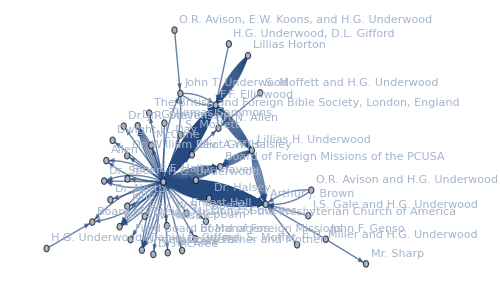

```mathematica
practicegragh=Graph[Thread[underwood2[[All,1]]->underwood2[[All, 2]]], VertexLabels -> "Name",ImageSize -> 500]
```

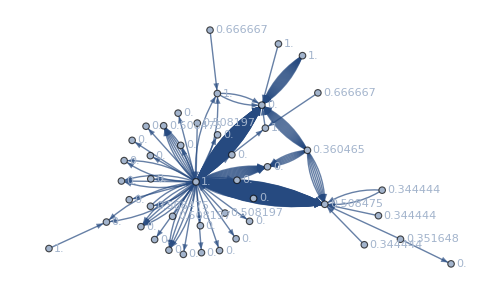

```mathematica
Graph[Thread[underwood2[[All,1]]->underwood2[[All, 2]]], VertexLabels -> "ClosenessCentrality",ImageSize -> 500]
```

Picking One Metric... is it no longer in the “more” options? Brace yourself for some “foul language” that gets the job done?

```mathematica
ClosenessCentrality[%]
```

{1.,0.,0.,0.,0.,0.,1.,1.,1.,0.508197,0.360465,0.,1.,0.,1.,0.,0.666667,0.508475,0.,0.,0.344444,0.344444,0.,0.,0.,0.508475,0.,0.508197,0.,0.,0.,0.,0.508475,0.,0.666667,0.,0.,0.,0.508197,0.351648,0.,0.,0.,0.344444,0.}

```mathematica
Part[VertexList[%4],Ordering[ClosenessCentrality[%4],All,Greater]]
```

{John T. Underwood,H.N. Allen,H.G. Underwood, D.L. Gifford,H.G. Underwood, Daniel L. Gifford, S. Moffet,Lillias Horton,H.G. Underwood,O.R. Avison, E.W. Koons, and H.G. Underwood,S. Moffett and H.G. Underwood,Dr. Goucher,John Fox,Arthur J. Brown,Thomas Sammons,Ernest Hall,Rev. W.H. Roberts,Lillias H. Underwood,John F. Genso,E.H. Miller and H.G. Underwood,J.S. Gale and H.G. Underwood,O.R. Avison and H.G. Underwood,Dr. North,Dr. Speer,Field Board of Managers,Mr. Sharp,Underwood's Father and Mother,J.S. Gale,McCune,Dr. J.F. Goucher,Dr. J.R. Stevenson,Dr. A.W. Halsey,Rev. E.F. Hall,Dr. William Elliot Griffis,Dwight H. Day,The British and Foreign Bible Society, London, England,Dr. Haven,Dr. Halsey,Dr. McAfee,S. Moffett,Rev. A.W. Halsley,Board of Foreign Missions of the PCUSA,Board of Foreign Missions,Mrs. Hepburn,Dr. Wells,Allen,Board of Foreign Missions of the Presbyterian Church of America,F.F. Ellinwood}

```mathematica
Sort[%6,Greater]
```

{1.,1.,1.,1.,1.,1.,0.666667,0.666667,0.508475,0.508475,0.508475,0.508197,0.508197,0.508197,0.360465,0.351648,0.344444,0.344444,0.344444,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Riffle[%7,%8]
```

{John T. Underwood,1.,H.N. Allen,1.,H.G. Underwood, D.L. Gifford,1.,H.G. Underwood, Daniel L. Gifford, S. Moffet,1.,Lillias Horton,1.,70,Mrs. Hepburn,0.,Dr. Wells,0.,Allen,0.,Board of Foreign Missions of the Presbyterian Church of America,0.,F.F. Ellinwood,0.}
 |  |  |  |

```mathematica
Partition[%,2]
```

{{John T. Underwood,1.},{H.N. Allen,1.},{H.G. Underwood, D.L. Gifford,1.},{H.G. Underwood, Daniel L. Gifford, S. Moffet,1.},37,{Dr. Wells,0.},{Allen,0.},{Board of Foreign Missions of the Presbyterian Church of America,0.},{F.F. Ellinwood,0.}}
 |  |  |  |

```mathematica
Take[%,10]
```

{{John T. Underwood,1.},{H.N. Allen,1.},{H.G. Underwood, D.L. Gifford,1.},{H.G. Underwood, Daniel L. Gifford, S. Moffet,1.},{Lillias Horton,1.},{H.G. Underwood,1.},{O.R. Avison, E.W. Koons, and H.G. Underwood,0.666667},{S. Moffett and H.G. Underwood,0.666667},{Dr. Goucher,0.508475},{John Fox,0.508475}}

```mathematica
Grid[%]
```

John T. Underwood | 1.
H.N. Allen | 1.
H.G. Underwood, D.L. Gifford | 1.
H.G. Underwood, Daniel L. Gifford, S. Moffet | 1.
Lillias Horton | 1.
H.G. Underwood | 1.
O.R. Avison, E.W. Koons, and H.G. Underwood | 0.666667
S. Moffett and H.G. Underwood | 0.666667
Dr. Goucher | 0.508475
John Fox | 0.508475

```mathematica
ReplacePart[%12,1->Prepend[First[%12],{"Name","Closeness Centrality"}]]
```

Name | Closeness Centrality
John T. Underwood | 1.
H.N. Allen | 1.
H.G. Underwood, D.L. Gifford | 1.
H.G. Underwood, Daniel L. Gifford, S. Moffet | 1.
Lillias Horton | 1.
H.G. Underwood | 1.
O.R. Avison, E.W. Koons, and H.G. Underwood | 0.666667
S. Moffett and H.G. Underwood | 0.666667
Dr. Goucher | 0.508475
John Fox | 0.508475

```mathematica
Insert[%13,Alignment->Left,2]
```

Name | Closeness Centrality
John T. Underwood | 1.
H.N. Allen | 1.
H.G. Underwood, D.L. Gifford | 1.
H.G. Underwood, Daniel L. Gifford, S. Moffet | 1.
Lillias Horton | 1.
H.G. Underwood | 1.
O.R. Avison, E.W. Koons, and H.G. Underwood | 0.666667
S. Moffett and H.G. Underwood | 0.666667
Dr. Goucher | 0.508475
John Fox | 0.508475

I am proud of this chart. But I need more data samples because it seems skewed.

```mathematica
Insert[%14,{Dividers->All,Spacings->1.5 {1,1}},2]
```

Name | Closeness Centrality
John T. Underwood | 1.
H.N. Allen | 1.
H.G. Underwood, D.L. Gifford | 1.
H.G. Underwood, Daniel L. Gifford, S. Moffet | 1.
Lillias Horton | 1.
H.G. Underwood | 1.
O.R. Avison, E.W. Koons, and H.G. Underwood | 0.666667
S. Moffett and H.G. Underwood | 0.666667
Dr. Goucher | 0.508475
John Fox | 0.508475

Trying to get a single year which is taking years from my life

```mathematica
Cases[underwood2,{__,__,1885.,___}]
```

{{H.G. Underwood,F.F. Ellinwood,1885.,1.,26.,Yokohama, Japan,Arrived in Korea (349)},6,{H.G. Underwood,F.F. Ellinwood,1885.,8.,31.,Seoul,}}
 |  |  |  |

I had some more foul language ... thank you for your help Bob Nachbar!

```mathematica
Cases[underwood2,{__,year_/;1885.≤year≤1888.,___}]
```

{{H.G. Underwood,F.F. Ellinwood,1885.,1.,26.,Yokohama, Japan,Arrived in Korea (349)},{H.G. Underwood,F.F. Ellinwood,1885.,2.,16.,Yokohama, Japan,Women missionaries are needed to witness to Korean women and male missionaries should be married (350).},44,{H.G. Underwood,F.F. Ellinwood,1888.,12.,23.,Seoul,}}
 |  |  |  |

Conclusion(s) and Confessions
1) I had to manually remove isolated nodes from the graph in Excel! This is not only inefficient regarding time and energy it is “losing” data. 
2) Because the data was removed in Excel I do not have a  way to  systematically ascertain how many of what types of “errors” were removed! 
3) Data removal and analysis became a mind-numbing  iterative process; doing the same thing again and again and hoping for a different result, is....
4) I originally wanted to do this assignment on the Horace Allen MSS, but because I kept finding more and more bad data in Excel, after a few hours I changed gears to a different set of missionary data.
5) I have PILES of “historical” data in Excel, that, if could be cleaned systematically and I could become more fluent in Mathematica, would be able to generate tests and may move SNA into other aspects of complexity science. 

My story continues in his-stories and His-story...